## Inputs. Everything is given in meV.

### Unit conversions

```mathematica
second =1/(6.58*10^-13);(* 1 second = this meV^-1*)
femsecond=10^-15 second; (* 1 fs = this meV^-1 *)
```

### Parameters

```mathematica
(*--Hamiltonian parameters--*)
Δa=0; (* atom detuning from laser *)
Δc=0; (* cavity detuning from laser *)
g=10.6*10^-6; (* light-matter coupling strength *)
Nm=10^10; (* number of molecules *)

g Sqrt[Nm]
Nb=0.0;
kT=25.68  ;(* cavity thermal occupation - assume zero cavity temperature *)

(*--Lindblad decay parameters--*)
nu=150;
amp=0.2
J[ω_]:= amp  Exp[-(ω/nu)^2]  ω;
Γd=0.0141; (* σ^- Lindblad rate: non-radiative decay *)
Γϕ= (Pi/ 4) J[g Sqrt[Nm]] Coth[(g Sqrt[Nm])/(  2 kT)] ;(* σ^z Lindblad rate: dephasing *)
κ=1/(120 femsecond) ;(* a Lindblad rate: cavity leakage *)


(*--Laser parameters--*)
σL=20 femsecond; (* laser width *)
η0=√Nm; (* laser amplitude *)
t0L=100 femsecond; (* laser central time *)
ηf[σL_,t0L_,t_]:=(η0/(σL*Sqrt[2*Pi])) Exp[-1/2((t-t0L)/σL)^2]; (* laser envelope function *)

(*--Simulation parameters--*)
tmax=6000femsecond+t0L;
```

1.06

0.2

## Cumulant expansion

### Initial state

```mathematica
(*Start with everything in the ground state and excite with Guassian pulse*)
a0=0; (* <a(0)> *)
aa0=0;(* <aa(0)> *)
da0=0; (* <a^†a(0)> *)
x0=({0,1}.({{0, 1}, {1, 0}}).{{0},{1}})⟦1⟧; (* <x(0)> *)
y0=({0,1}.({{0, -ⅈ}, {ⅈ, 0}}).{{0},{1}})⟦1⟧; (* <y(0)> *)
z0=({0,1}.({{1, 0}, {0, -1}}).{{0},{1}})⟦1⟧; (* <z(0)> *)
```

### Equations of motion

```mathematica
(* x,y,z=σ^(x,y,z); a=a; d=a^†; n here is the number of molecules (NOT number of photons) *)
```

```mathematica
(* first order *)
Da[a_,x_,y_,κ_,g_,n_,η_]:=-(ⅈ Δc+1/2 κ(1+Nb)-1/2 κ Nb)a- g/2 n (ⅈ x+y)+η;
Dx[x_,y_,az_,Γt_,g_]:=-Δa y-Γt x-2 g Im[az];
Dy[x_,y_,az_,Γt_,g_]:=Δa x-2 g Re[az]-Γt y;
Dz[z_,ax_,ay_,Γd_,g_]:=2g (Re[ay]+Im[ax])-Γd(z+1);

(* second order *)
Dda[a_,da_,ax_,ay_,κ_,g_,n_,η_]:=κ Nb(1+da)-κ(1+Nb)da-g n(Im[ax]+Re[ay])+2η Re[a];
Daa[a_,aa_,ax_,ay_,κ_,g_,n_,η_]:=-(2ⅈ Δc+κ(1+Nb)-κ Nb)aa- g n (ⅈ ax+ay)+2 η a;
Dax[x_,z_,ax_,ay_,xx_,xy_,aaz_,daz_,κ_,Γt_,g_,n_,η_]:=-(ⅈ Δc+1/2 κ(1+Nb)-1/2 κ Nb+Γt)ax-Δa ay-ⅈ g/2 (1+(n-1) xx)-g/2(ⅈ z+(n-1)xy)+ⅈ g(aaz-daz)+η x;
Day[y_,z_,ay_,ax_,xy_,yy_,aaz_,daz_,κ_,Γt_,g_,n_,η_]:=-(ⅈ Δc+1/2 κ(1+Nb)-1/2 κ Nb+Γt)ay+Δa ax-ⅈ g/2(-ⅈ z+(n-1)xy)-g/2(1+(n-1)yy)-g(aaz+daz)+η y;
Daz[a_,x_,y_,z_,az_,xz_,yz_,aax_,dax_,aay_,day_,κ_,Γd_,g_,n_,η_]:=-(ⅈ Δc+1/2 κ(1+Nb)-1/2 κ Nb)az-g/2(-ⅈ x+(n-1)yz)-ⅈ g/2(ⅈ y+(n-1)xz)+g(aay+day)-ⅈ g(aax-dax)-Γd(az+a)+η z;
Dxx[xx_,xy_,axz_,Γt_,g_]:=-2Δa xy-4 g Im[axz]-2Γt xx;
Dyy[xy_,yy_,ayz_,Γt_,g_]:=2 Δa xy-2Γt yy-4g Re[ayz];
Dzz[z_,zz_,axz_,ayz_,Γd_,g_]:=4 g (Im[axz]+ Re[ayz])-2Γd(zz+z);
Dxy[xx_,xy_,yy_,axz_,ayz_,Γt_,g_]:=Δa(xx-yy)-2 g (Re[axz]+Im[ayz])-2Γt xy;
Dxz[x_,xz_,yz_,axy_,axx_,azz_,Γt_,Γd_,g_]:=-Δa yz+2g (Re[axy]+Im[axx]-Im[azz])-Γt xz-Γd(xz+x);
Dyz[y_,xz_,yz_,axy_,ayy_,azz_,Γt_,Γd_,g_]:=Δa xz+2g(Re[ayy]-Re[azz]+Im[axy])-Γt yz-Γd(yz+y);

(* Γtilde *)
Γtf[Γϕ_,Γd_]:=2 Γϕ+1/2 Γd;
```

### Truncation at third order: <<abc>>=<abc>-<ab><c>-<a><bc>-<ac><b>+2<a><b><c>=0

```mathematica
axx[t_]:=ax[t]*x[t]+a[t]*xx[t]+ax[t]*x[t]-2a[t]*x[t]*x[t];
axy[t_]:=ax[t]*y[t]+a[t]*xy[t]+ay[t]*x[t]-2a[t]*x[t]*y[t];
axz[t_]:=ax[t]*z[t]+a[t]*xz[t]+az[t]*x[t]-2a[t]*x[t]*z[t];
ayy[t_]:=ay[t]*y[t]+a[t]*yy[t]+ay[t]*y[t]-2a[t]*y[t]*y[t];
ayz[t_]:=ay[t]*z[t]+a[t]*yz[t]+az[t]*y[t]-2a[t]*y[t]*z[t];
azz[t_]:=az[t]*z[t]+a[t]*zz[t]+az[t]*z[t]-2a[t]*z[t]*z[t];
aax[t_]:=aa[t]*x[t]+a[t]*ax[t]+ax[t]*a[t]-2a[t]*a[t]*x[t];
aay[t_]:=aa[t]*y[t]+a[t]*ay[t]+ay[t]*a[t]-2a[t]*a[t]*y[t];
aaz[t_]:=aa[t]*z[t]+a[t]*az[t]+az[t]*a[t]-2a[t]*a[t]*z[t];
dax[t_]:=da[t]*x[t]+Conjugate[a[t]]*ax[t]+Conjugate[ax[t]]*a[t]-2Conjugate[a[t]]*a[t]*x[t];
day[t_]:=da[t]*y[t]+Conjugate[a[t]]*ay[t]+Conjugate[ay[t]]*a[t]-2Conjugate[a[t]]*a[t]*y[t];
daz[t_]:=da[t]*z[t]+Conjugate[a[t]]*az[t]+Conjugate[az[t]]*a[t]-2Conjugate[a[t]]*a[t]*z[t];
```

### Functions to solve

```mathematica
sol[κ_,Γt_,Γd_,g_,n_,σL_,t0L_,tmax_]:=NDSolve[{D[a[t],t]==Da[a[t],x[t],y[t],κ,g,n,ηf[σL,t0L,t]],D[x[t],t]==Dx[x[t],y[t],az[t],Γt,g],D[y[t],t]==Dy[x[t],y[t],az[t],Γt,g],D[z[t],t]==Dz[z[t],ax[t],ay[t],Γd,g],D[da[t],t]==Dda[a[t],da[t],ax[t],ay[t],κ,g,n,ηf[σL,t0L,t]],D[aa[t],t]==Daa[a[t],aa[t],ax[t],ay[t],κ,g,n,ηf[σL,t0L,t]],D[ax[t],t]== Dax[x[t],z[t],ax[t],ay[t],xx[t],xy[t],aaz[t],daz[t],κ,Γt,g,n,ηf[σL,t0L,t]],D[ay[t],t]== Day[y[t],z[t],ay[t],ax[t],xy[t],yy[t],aaz[t],daz[t],κ,Γt,g,n,ηf[σL,t0L,t]],D[az[t],t]== Daz[a[t],x[t],y[t],z[t],az[t],xz[t],yz[t],aax[t],dax[t],aay[t],day[t],κ,Γd,g,n,ηf[σL,t0L,t]],D[xx[t],t]==Dxx[xx[t],xy[t],axz[t],Γt,g],D[yy[t],t]==Dyy[xy[t],yy[t],ayz[t],Γt,g],D[zz[t],t]==Dzz[z[t],zz[t],axz[t],ayz[t],Γd,g],D[xy[t],t]==Dxy[xx[t],xy[t],yy[t],axz[t],ayz[t],Γt,g],D[xz[t],t]==Dxz[x[t],xz[t],yz[t],axy[t],axx[t],azz[t],Γt,Γd,g],D[yz[t],t]==Dyz[y[t],xz[t],yz[t],axy[t],ayy[t],azz[t],Γt,Γd,g],a[0]== a0,x[0]==x0,y[0]==y0,z[0]==z0,aa[0]==aa0,da[0]==da0,ax[0]==a0*x0,ay[0]==a0*y0,az[0]==a0*z0,xx[0]==x0^2,xy[0]==x0*y0,xz[0]==x0*z0,yy[0]==y0^2,yz[0]==y0*z0,zz[0]==z0*z0},{a,x,y,z,da,aa,ax,ay,az,xx,xy,xz,yy,yz,zz},{t,0,tmax},Method->"StiffnessSwitching"];
```

## Calculate <σ^z(t)> and n=<a^†a(t)>

### Generate plots

```mathematica
taxis=Table[-t0L+i,{i,0,tmax,1}];
soln=sol[κ,Γtf[Γϕ/.amp->0.01,Γd],Γd,g,Nm,σL,t0L,tmax];
zv[t_]:=Re[z[t]]/.soln;
dav[t_]:=Re[da[t]]/.soln;
```

### Plot

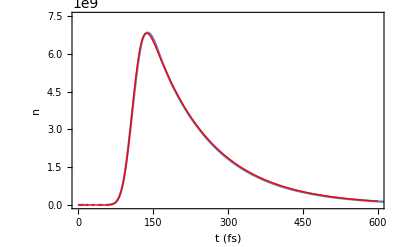

```mathematica
TimeArray=BinaryReadList["/Users/ferguswilliams/Downloads/jk/examples/time.dat","Real64"];
SigzArray=BinaryReadList["/Users/ferguswilliams/Downloads/jk/examples/sig.dat", "Real64"];
AlphaArray=BinaryReadList["/Users/ferguswilliams/Downloads/jk/examples/alph.dat", "Real64"];
datalph=Table[{TimeArray[[i]],AlphaArray[[i]]},{i,1,Length[TimeArray]}];
datsigz=Table[{TimeArray[[i]],SigzArray[[i]]},{i,1,Length[TimeArray]}];
Plot[dav[t*femsecond],{t,0,tmax/femsecond},Frame->True,PlotRange->{{0,Last[TimeArray]},{0,1.1*Max[AlphaArray]}},FrameLabel->{"t (fs)","n"},LabelStyle->Directive[Black,15],Epilog->{Red,Line[datalph]}]
```

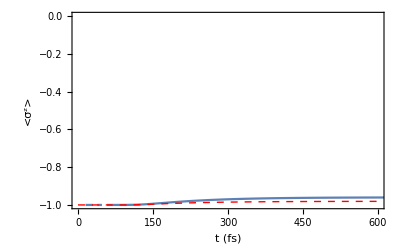

```mathematica
Plot[zv[t*femsecond],{t,0,tmax/femsecond},Frame->True,Epilog->{Directive[Red,Dashed],Line[datsigz]},PlotRange->{{0,TimeArray[[-1]]},{-1,-0.0}},FrameLabel->{"t (fs)","<σ^z>"},LabelStyle->Directive[Black,15]]
```